Landau integral:

```mathematica
1/(√π)∫_(-∞)^∞ (ϵ^(-x^2))/(x-ζ) ⅆx
```

ConditionalExpression[-(ϵ^(-ζ^2) (π Erfi[ζ √Log[ϵ]]-Log[-1/ζ]+Log[1/ζ]))/(√π), (Re[ζ]==0||ζ∉ℝ)&&Re[Log[ϵ]]>0]

```mathematica
Z = Re[N[1/(√π)Integrate[Exp[-x^2]/(x-1.7/(0.6 * √2)-10^-5 I),{x,-∞,∞}]]]
```

-0.601257

```mathematica
1-(1/0.6)^2(0.7/0.6 Z-(0.2-1)(1+1.7/0.6 Z))
```

4.51199

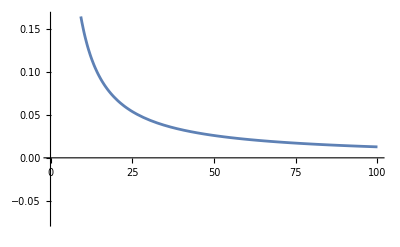

```mathematica
Plot[(√(π/2)+1/a)/(a-1),{a,10^-2,10^2}]
```

Setting the parameters of our run
(1) Hunana, P.; Zank, G. P. On the Parallel and Oblique Firehose Instability in Fluid Models. ApJ 2017, 839 (1), 13. https://doi.org/10.3847/1538-4357/aa64e3.

```mathematica
n=1 10^6; e = 1.602176634×10^-19; me = 9.1093837139×10^-31;ϵ=8.8541878188×10^-12; c=299792458; mi = 1.67262192595 10^-27; μ = 1.25663706127 10^-6;Fe = 48.5/√1.5
```

39.6001

```mathematica
n=1.5 10^6; e = 1.602176634×10^-19; me = 9.1093837139×10^-31;ϵ=8.8541878188×10^-12; c=299792458; mi = 1.67262192595 10^-27; μ = 1.25663706127 10^-6;1/(2 π)√((n e^2)/(me ϵ))
```

10996.6

Important constants:

```mathematica
10^6 4 π^2 me ϵ/e^2
```

12404.4

```mathematica
(c^2 me)/(2 e 1000)
```

255.499

Input frequency and temperature for WHAMP

```mathematica
Fe = 48.5;Ti = 5; Omegae = 2π Fe;Omegai=Omegae me/mi; B = me Omegae/e;VA=B/(√(μ n mi))1/c
```

0.000102927

```mathematica
Omegai/(2π)/1000
```

0.0000264139

```mathematica
Vth=1/c √(2 e Ti/mi)
```

0.000103237

Resulting plasma beta

```mathematica
Vth^2/VA^2
```

1.00603

Solving dispersion relation:

```mathematica
Solve[k/ω==-(Ω/Subscript[V, A])/(ω-Ω),ω]
```

{{ω→(k Ω V_A)/(Ω+k V_A)}}

```mathematica
Solve[k^2/ω^2==(Ω/Subscript[V, A])/(ω+Ω),ω]
```

{{ω→-(-k^2 V_A+k √V_A √(4 Ω^2+k^2 V_A))/(2 Ω)},{ω→(k^2 V_A+k √V_A √(4 Ω^2+k^2 V_A))/(2 Ω)}}

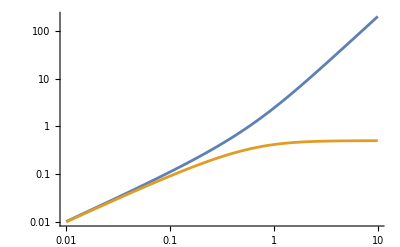

```mathematica
LogLogPlot[{k^2+k √(1+k^2),-k^2+k √(1+k^2)},{k,10^-2,10}]
```

The inputs to WHAMP together with outputs:
╰─ ./whamp  -file ../Models/H17f1
╰─ ./whamp  -file ../Models/H17f1a

# TOTAL PLASMA FREQ.:   10.99931 KHZ; SPEC 1 GYRO FREQ.:   0.00003 KHZ; SPEC 1 PLASMA FREQ.:    0.25663 KHZ; 
# SPECIES 1 parallel V_TH/C:   0.000103;  SPECIES 1 parallel BETA:   1.005986
# H+   DN= 1.50000E+06  T=  0.00500  D=1.00  A=1.00  B=0.00 VD= 0.00
# e-   DN= 1.50000E+06  T=  0.00000  D=1.00  A=1.00  B=0.00 VD= 0.00
#INPUT: 
 
p0z.1f.1
#OUTPUT: 

pzf/e
    0.0000000      0.1000000    1.0695170E-01 -5.77E-09    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000

This is right hand polarized wave, corresponding to whistler branch. We get a value that is very close to the CGL+FLR computation. 

#INPUT: 
  
l1
    1.0000000      1.2589254    2.9318801E+00 -5.85E-02    
 EX= 0.7487  0.0000  EY= 0.0369  0.6618  EZ= 0.0004  0.0001   

#INPUT: 
  
p-10z-1f.1
    0.0000000      0.1000000    1.0695170E-01 -5.77E-09    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000  0.0000   

#INPUT: 
  
z-1,1,.6666
    0.0000000      0.1000000    1.0695170E-01 -5.77E-09    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000  0.0000   
    0.0000000      0.4640876    6.1175614E-01 -2.12E-05    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ= 0.0000  0.0000   
    0.0000000      2.1537732    5.4987867E+00 -4.92E-04    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ= 0.0000  0.0000   
    0.0000000      9.9953951    9.5112645E+01  3.68E-09    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ= 0.0000 -0.0000   

These values seem consistent with the whistler branch (blue) that we see

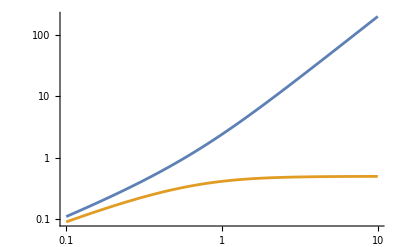

```mathematica
LogLogPlot[{k^2+k √(1+k^2),-k^2+k √(1+k^2)},{k,10^-1,10}]
```

We may try to jump onto ion cyclotron branch (orange in plot, red in text) which is left hand polarized Ey = -i √2 but it seems that it only works for the first entry:

#INPUT: 
  
f.089
    0.0000000      0.1000000    9.1947478E-02  1.10E-08    
 EX= 0.7071  0.0000  EY= 0.0000 -0.7071  EZ= 0.0000 -0.0000   
    0.0000000      0.4640876    6.1175614E-01 -2.12E-05    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ= 0.0000  0.0000   
    0.0000000      2.1537732    5.4987867E+00 -4.92E-04    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ= 0.0000  0.0000   
    0.0000000      9.9953951    9.5112645E+01  3.68E-09    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ= 0.0000 -0.0000

This is frustrating because we are providing small guess for initial frequency yet, the program still chooses to output whistler mode rather than ion-cyclotron in the three other cases

#INPUT: 
  
l0p0z.1f.04
    0.0000000      0.1000000    9.1947289E-02  1.10E-08    
 EX= 0.7071  0.0000  EY= 0.0000 -0.7071  EZ= 0.0000 -0.0000   
p0z.05f.04
    0.0000000      0.0500000    4.7941644E-02 -5.77E-10    
 EX= 0.7071  0.0000  EY= 0.0000 -0.7071  EZ= 0.0000 -0.0000  
p0z.2f.04
    0.0000000      0.2000000    1.6679361E-01 -2.35E-06    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000  0.0000   
 p0z.4f.1
    0.0000000      0.4000000    2.4331412E-01 -2.20E-02    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000 -0.0000    
p0z.5f.1
    0.0000000      0.5000000    2.6139770E-01 -6.58E-02    
 EX= 0.7071  0.0000  EY= 0.0000 -0.7071  EZ= 0.0000 -0.0000  
 p0z.5f2e-1
    0.0000000      0.5000000    2.6139770E-01 -6.58E-02    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000  0.0000  
p0z.6f.1
    0.0000000      0.6000000    8.4548972E-01 -2.60E-04    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000 -0.0000  
  
  Here we see that for some reason we diverge from the branch. We can go back to the case that worked and try modifying the frequency guess, to see how it can fail. We are going to scan the initial frequency guess:

  #INPUT: 
 f2e-2
    0.0000000      0.5000000    6.7111519E-01 -4.84E-05    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000  
f5e-2
  NO CONVERGENCE!
  KP= 0.000  KZ=0.5000  X=    0.32E+00   -0.42E+00
  I= 15  IRK=  1

  TOO HEAVILY DAMPED!
    
f8e-2
    0.0000000      0.5000000    2.6139770E-01 -6.58E-02    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000  0.0000   
 f2e-1
    0.0000000      0.5000000    2.6139770E-01 -6.58E-02    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000  0.0000   
f3e-1
    0.0000000      0.5000000    6.7111519E-01 -4.84E-05    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000 
 
When f is too high we of course jump again to the whistler branch, but if we choose a value that is too small we again get the whistler branch surprisingly
f2e-1
    0.0000000      0.5100000    2.6315115E-01 -7.11E-02    
 EX= 0.7071  0.0000  EY= 0.0000 -0.7071  EZ= 0.0000 -0.0000
z.51f2.2e-1
    0.0000000      0.5100000    2.6315115E-01 -7.11E-02    
 EX= 0.7071  0.0000  EY=-0.0000 -0.7071  EZ=-0.0000  0.0000   
 z.51f2.3e-1
  NO CONVERGENCE!
  z.52f2e-1
  NO CONVERGENCE!

My understanding is that at this point there is too much damping, but I am wondering how Hunana and Zank were able to plot the dispersion relation using WHAMP, possibly modifying the code itself?

Hall - CGL - FLR3 model

```mathematica
n=1 10^6; e = 1.602176634×10^-19; me = 9.1093837139×10^-31;ϵ=8.8541878188×10^-12; c=299792458; mi = 1.67262192595 10^-27; μ = 1.25663706127 10^-6;Fe = 19.86; Ti = 5; Omegae = 2π Fe;Omegai=Omegae me/mi; B = me Omegae/e;VA=B/(√(μ n mi))1/c;Vth=1/c √(2 e Ti/mi);beta =Vth^2/VA^2
```

3.99986

```mathematica
a=2;vb = beta (1-a/2); va = 1+beta/2(a-1)
```

2.99993

In the expression below k is scaled using d_i which basically means V_A/Omega

```mathematica
Om[k_]:=1/(1+vb k^2)(k^2/2(1+vb (1+k^2)+k^2)beta^2(3/2-a))+k√((va^2-beta/2 k^2(1+beta(1-a))+beta^2/2(a-2)k^4)(1+vb k^2)+k^2/4(1+vb(1+k^2)+k^2 beta^2(3/2-a))^2)
```

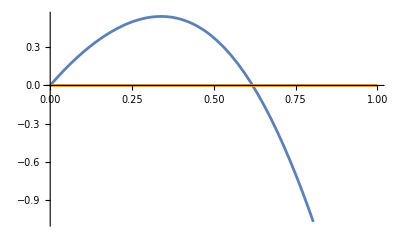

```mathematica
Plot[{Re[Om[k]],Im[Om[k]]},{k,10^-3,1}]
```

To get firehose unstable region we require:

```mathematica
a=0.49;vb = beta (1-a/2); va = 1+beta/2(a-1);Om[k_]:=+1/(1+vb k^2)(k^2/2(1+vb (1+k^2)+k^2)beta^2(3/2-a))+k√((va^2-beta/2 k^2(1+beta(1-a))+beta^2/2(a-2)k^4)(1+vb k^2)+k^2/4(1+vb(1+k^2)+k^2 beta^2(3/2-a))^2)
```

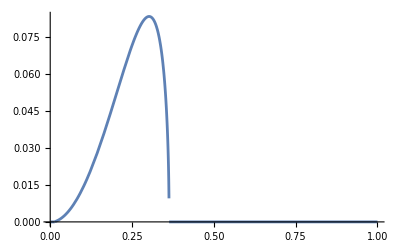

```mathematica
Plot[Im[Om[k]],{k,10^-3,1}]
```

```mathematica
LogLogPlot[Re[Om[k]],{k,10^-3,1}]
```

-Graphics-

```mathematica
a=0.49;Om[k_]:=k^2/2(1+beta (1-a/2))+k √(1+beta/2(a-1)+k^2/4(1-beta(1-a/2))^2)
```

Let’s choose k V_A/Omega = 0.2, which for √beta=2 implies k V_th/Omega = 0.4

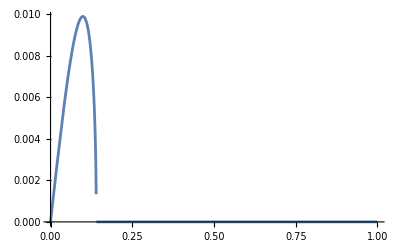

```mathematica
Plot[Im[Om[k]],{k,0,1}]
```

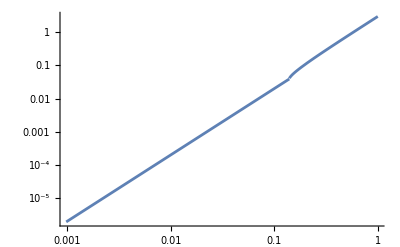

```mathematica
LogLogPlot[Re[Om[k]],{k,0,1}]
```

So it is interesting to look at k V_A/Omega ~ 0.1, but that is k V_th/Omega ~ 0.2
  ./whamp  -file ../Models/H17f3b 
# TOTAL PLASMA FREQ.:    8.98090 KHZ; SPEC 1 GYRO FREQ.:   0.00001 KHZ; SPEC 1 PLASMA FREQ.:    0.20953 KHZ; 
# SPECIES 1 parallel V_TH/C:   0.000103;  SPECIES 1 parallel BETA:   3.999683
# H+   DN= 1.00000E+06  T=  0.00500  D=1.00  A=0.49  B=0.00 VD= 0.00
# e-   DN= 1.00000E+06  T=  0.00000  D=1.00  A=1.00  B=0.00 VD= 0.00
#INPUT: 
  
p0z2f.1
#OUTPUT: 

pzf/e
    0.0000000      2.0000000    1.6504716E+00 -5.69E-02    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000  0.0000   
p0z.2f1e-3
    0.0000000      0.2000000    2.0656351E-02  2.02E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000   
p0z.6f1e-3
    0.0000000      0.6000000    2.4688253E-01  8.96E-02    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000 -0.0000   
 #INPUT: 
  
z.2,.9,.1            
    0.0000000      0.2000000    2.0656351E-02  2.02E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.3000000    4.8935979E-02  4.01E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.4000000    9.8232505E-02  6.57E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.5000000    1.6778669E-01  8.32E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ= 0.0000 -0.0000   
    0.0000000      0.6000000    2.4688252E-01  8.96E-02    
 EX= 0.7071  0.0000  EY= 0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.7000000    3.3044283E-01  8.81E-02    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.8000000    4.1672102E-01  8.15E-02    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000 -0.0000   
    0.0000000      0.9000000    5.0517181E-01  7.17E-02    
 EX= 0.7071  0.0000  EY=-0.0000  0.7071  EZ=-0.0000  0.0000

Now it is possible to converge where the algorithm was failing:
 ./whamp -file ../Models/H17f3b 
# TOTAL PLASMA FREQ.:    8.98090 KHZ; SPEC 1 GYRO FREQ.:   0.00001 KHZ; SPEC 1 PLASMA FREQ.:    0.20953 KHZ; 
# SPECIES 1 parallel V_TH/C:   0.000103;  SPECIES 1 parallel BETA:   3.999683
# H+   DN= 1.00000E+06  T=  0.00500  D=1.00  A=0.49  B=0.00 VD= 0.00
# e-   DN= 1.00000E+06  T=  0.00000  D=1.00  A=1.00  B=0.00 VD= 0.00
#INPUT: 
  
p0z.1f1e-3
#OUTPUT: 

pzf
  NO CONVERGENCE!
  KP= 0.000  KZ=0.1000  X=    0.86E+02    0.39E+03
  I= 51  IRK=  1
./whamp -maxiterations 200  -file ../Models/H17f3b
# TOTAL PLASMA FREQ.:    8.98090 KHZ; SPEC 1 GYRO FREQ.:   0.00001 KHZ; SPEC 1 PLASMA FREQ.:    0.20953 KHZ; 
# SPECIES 1 parallel V_TH/C:   0.000103;  SPECIES 1 parallel BETA:   3.999683
# H+   DN= 1.00000E+06  T=  0.00500  D=1.00  A=0.49  B=0.00 VD= 0.00
# e-   DN= 1.00000E+06  T=  0.00000  D=1.00  A=1.00  B=0.00 VD= 0.00
#INPUT: 
  
p0z.1f1e-3
#OUTPUT: 

pzf
    0.0000000      0.1000000    8.3122224E+05 -1.15E-06